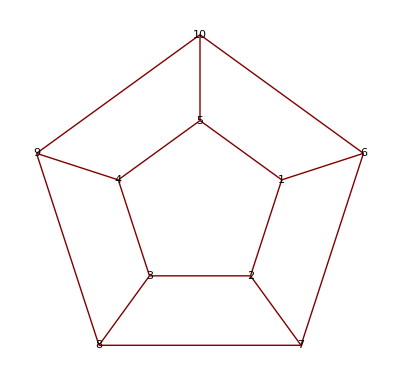

(0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0)

```mathematica
Needs["GraphUtilities`"];
g=PetersenGraph[5,1];
GraphPlot[g,VertexLabeling->True]
Normal[AdjacencyMatrix[g]]//MatrixForm
LineGraph[g];
GraphDistanceMatrix[g]//MatrixForm;
```

```mathematica
({{0, 1, 0, 0, 1, 1, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 1, 0, 0, 0}, {0, 1, 0, 1, 0, 0, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0, 0, 0, 1, 0}, {1, 0, 0, 1, 0, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 1, 0, 0, 1}, {0, 1, 0, 0, 0, 1, 0, 1, 0, 0}, {0, 0, 1, 0, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 1, 1, 0, 0, 1, 0}})
```

```mathematica
Subgraph[g,{1,5,6,10}]
HamiltonianCycles[%]
```

-Graphics-

{{1,5,10,6}}

```mathematica
Sort[{1,5,6,10}]==Sort[{1,5,10,6}]
```

True

```mathematica
{{1,2,3,4,5}}=={{1,2,3,4,5}}
```

True

```mathematica
sel[list_]:=Table[Table[list[[i]]*PadLeft[IntegerDigits[x,2],Length[list]][[i]],{i,1,Length[list]}],{x,1,2^Length[list]-1}]
n0[list_]:=Delete[list,Position[list,0]]
```

```mathematica
Map[n0,sel[{1,2,3}]]
```

{{3},{2},{2,3},{1},{1,3},{1,2},{1,2,3}}

```mathematica
gint[x_,y_]:=VertexList[x]∩VertexList[y]
```

```mathematica
gint[Subgraph[g,{1,5,6,10}],Subgraph[g,{1,2,3,4,5}]]
```

{1,5}

```mathematica
"Gives all subcycles of g with verteces from 1-10:";
gg=Delete[DeleteDuplicates[Monitor[Table[Piecewise[{{Subgraph[g,i], Sort[i]==Sort[Flatten[HamiltonianCycles[Subgraph[g,i]]]]}, {0, True}}],{i,Map[n0,sel[{1,2,3,4,5,6,7,8,9,10}]]}],i]],1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

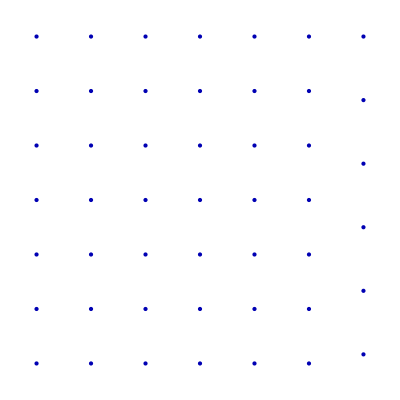

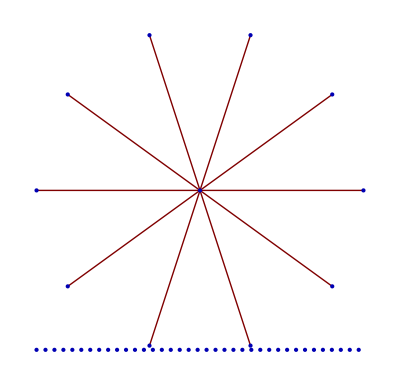

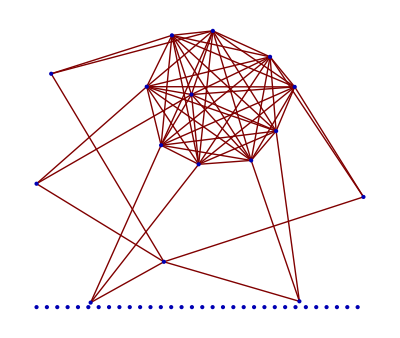

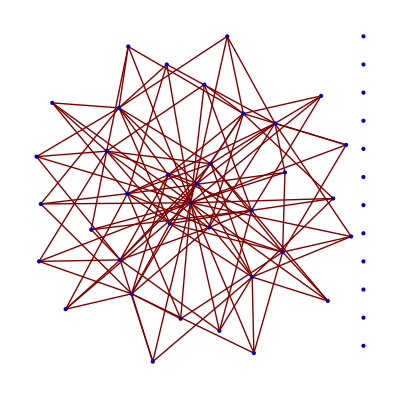

```mathematica
T=GraphPlot[Table[Piecewise[{{1, Length[gint[gg[[i]],gg[[j]]]]==10}, {0, True}}],{i,1,Length[gg]},{j,1,Length[gg]}]]
```

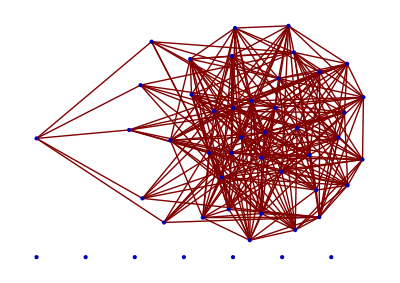

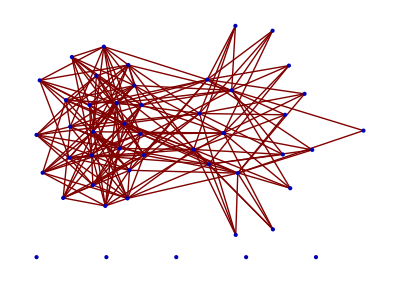

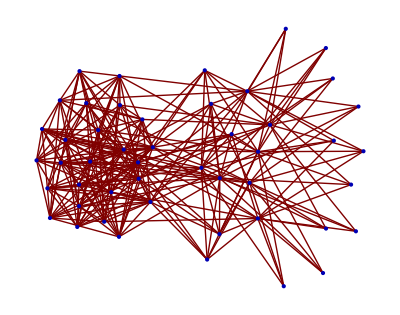

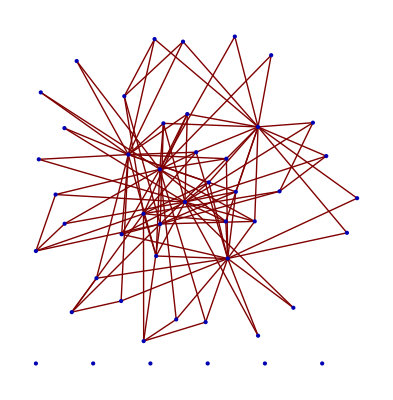

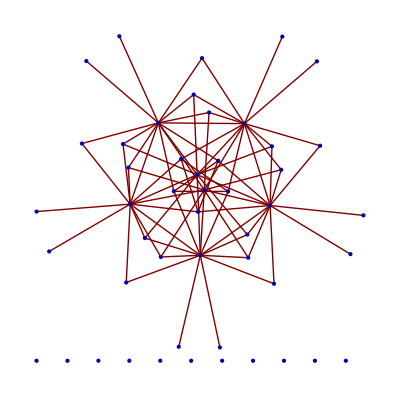

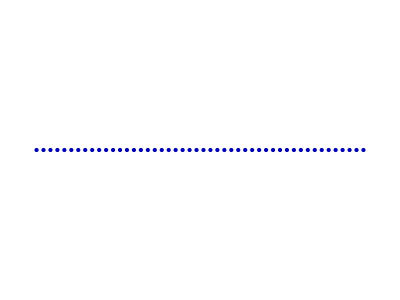

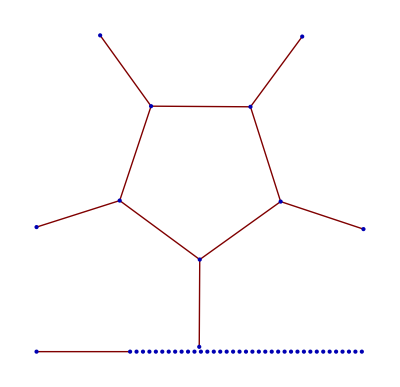

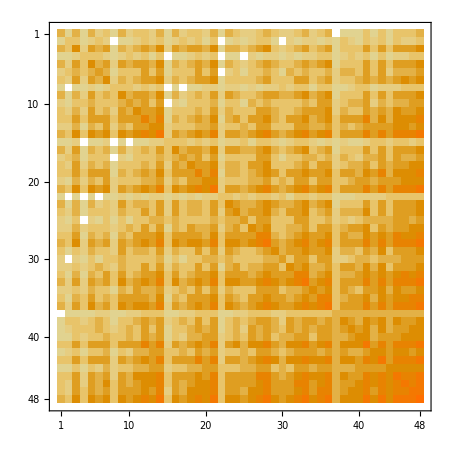

```mathematica
MatrixPlot[({{5, 2, 5, 2, 5, 3, 4, 2, 5, 3, 4, 4, 3, 5, 2, 5, 3, 4, 4, 3, 5, 2, 5, 4, 3, 3, 4, 5, 4, 3, 3, 4, 5, 3, 4, 5, 0, 2, 2, 2, 4, 2, 4, 2, 4, 4, 4, 5}, {2, 4, 4, 2, 3, 4, 3, 0, 2, 2, 3, 4, 3, 4, 2, 3, 4, 3, 4, 2, 4, 0, 2, 3, 2, 3, 4, 4, 2, 0, 3, 2, 3, 3, 2, 3, 2, 4, 3, 2, 4, 3, 4, 2, 4, 3, 3, 4}, {5, 4, 7, 3, 6, 5, 6, 2, 5, 4, 5, 6, 5, 7, 3, 6, 5, 6, 6, 5, 7, 2, 5, 5, 4, 5, 6, 7, 4, 3, 4, 5, 6, 4, 5, 6, 2, 4, 4, 4, 6, 4, 6, 4, 6, 6, 6, 7}, {2, 2, 3, 4, 4, 4, 3, 2, 3, 4, 3, 4, 2, 4, 0, 2, 2, 3, 4, 3, 4, 0, 2, 2, 0, 3, 2, 3, 3, 2, 3, 2, 3, 3, 4, 4, 2, 3, 4, 3, 4, 2, 4, 2, 3, 3, 4, 4}, {5, 3, 6, 4, 7, 5, 6, 3, 6, 5, 6, 6, 5, 7, 2, 5, 4, 5, 6, 5, 7, 2, 5, 4, 3, 4, 5, 6, 5, 4, 4, 5, 6, 5, 6, 7, 2, 4, 4, 4, 6, 4, 6, 4, 6, 6, 6, 7}, {3, 4, 5, 4, 5, 6, 5, 2, 4, 4, 4, 6, 4, 6, 2, 4, 4, 4, 6, 4, 6, 0, 3, 4, 2, 4, 4, 5, 4, 2, 5, 4, 5, 4, 4, 5, 3, 5, 5, 4, 6, 4, 6, 3, 5, 5, 5, 6}, {4, 3, 6, 3, 6, 5, 7, 3, 5, 4, 5, 6, 6, 7, 3, 5, 4, 5, 6, 6, 7, 2, 4, 4, 4, 4, 5, 6, 4, 4, 4, 6, 6, 4, 5, 6, 3, 4, 4, 5, 6, 5, 6, 5, 6, 7, 6, 7}, {2, 0, 2, 2, 3, 2, 3, 4, 4, 4, 3, 4, 3, 4, 0, 2, 0, 2, 2, 3, 3, 2, 3, 3, 2, 3, 2, 3, 3, 4, 3, 4, 4, 2, 4, 4, 2, 2, 3, 4, 4, 2, 3, 3, 3, 4, 4, 4}, {5, 2, 5, 3, 6, 4, 5, 4, 7, 5, 6, 6, 5, 7, 2, 5, 3, 4, 5, 4, 6, 3, 6, 5, 4, 4, 5, 6, 6, 5, 5, 6, 7, 5, 6, 7, 2, 4, 4, 4, 6, 4, 6, 4, 6, 6, 6, 7}, {3, 2, 4, 4, 5, 4, 4, 4, 5, 6, 5, 6, 4, 6, 0, 3, 2, 4, 4, 4, 5, 2, 4, 4, 2, 5, 4, 5, 4, 4, 4, 4, 5, 4, 6, 6, 3, 4, 5, 5, 6, 3, 5, 4, 5, 5, 6, 6}, {4, 3, 5, 3, 6, 4, 5, 3, 6, 5, 7, 6, 6, 7, 2, 4, 4, 4, 5, 4, 6, 3, 5, 4, 4, 4, 6, 6, 5, 4, 4, 5, 6, 6, 6, 7, 3, 5, 4, 4, 6, 5, 6, 5, 7, 6, 6, 7}, {4, 4, 6, 4, 6, 6, 6, 4, 6, 6, 6, 8, 6, 8, 2, 5, 4, 5, 6, 5, 7, 2, 5, 6, 4, 6, 6, 7, 5, 4, 6, 6, 7, 5, 6, 7, 4, 6, 6, 6, 8, 5, 7, 5, 7, 7, 7, 8}, {3, 3, 5, 2, 5, 4, 6, 3, 5, 4, 6, 6, 7, 7, 3, 4, 4, 4, 5, 5, 6, 3, 4, 4, 5, 4, 6, 6, 4, 4, 4, 6, 6, 5, 5, 6, 4, 5, 4, 5, 6, 6, 6, 6, 7, 7, 6, 7}, {5, 4, 7, 4, 7, 6, 7, 4, 7, 6, 7, 8, 7, 9, 3, 6, 5, 6, 7, 6, 8, 3, 6, 6, 5, 6, 7, 8, 6, 5, 6, 7, 8, 6, 7, 8, 4, 6, 6, 6, 8, 6, 8, 6, 8, 8, 8, 9}, {2, 2, 3, 0, 2, 2, 3, 0, 2, 0, 2, 2, 3, 3, 4, 4, 4, 3, 4, 3, 4, 2, 3, 3, 4, 2, 4, 4, 3, 2, 3, 4, 4, 3, 2, 3, 2, 3, 2, 2, 3, 4, 4, 3, 4, 4, 3, 4}, {5, 3, 6, 2, 5, 4, 5, 2, 5, 3, 4, 5, 4, 6, 4, 7, 5, 6, 6, 5, 7, 3, 6, 6, 5, 5, 6, 7, 5, 4, 5, 6, 7, 4, 5, 6, 2, 4, 4, 4, 6, 4, 6, 4, 6, 6, 6, 7}, {3, 4, 5, 2, 4, 4, 4, 0, 3, 2, 4, 4, 4, 5, 4, 5, 6, 5, 6, 4, 6, 2, 4, 4, 4, 4, 6, 6, 4, 2, 4, 4, 5, 5, 4, 5, 3, 5, 4, 3, 5, 5, 6, 4, 6, 5, 5, 6}, {4, 3, 6, 3, 5, 4, 5, 2, 4, 4, 4, 5, 4, 6, 3, 6, 5, 7, 6, 6, 7, 3, 5, 5, 4, 6, 6, 7, 4, 4, 4, 5, 6, 4, 6, 6, 3, 4, 5, 5, 6, 4, 6, 5, 6, 6, 7, 7}, {4, 4, 6, 4, 6, 6, 6, 2, 5, 4, 5, 6, 5, 7, 4, 6, 6, 6, 8, 6, 8, 2, 5, 5, 4, 5, 6, 7, 6, 4, 6, 6, 7, 6, 6, 7, 4, 6, 6, 5, 7, 6, 8, 5, 7, 7, 7, 8}, {3, 2, 5, 3, 5, 4, 6, 3, 4, 4, 4, 5, 5, 6, 3, 5, 4, 6, 6, 7, 7, 3, 4, 4, 4, 5, 5, 6, 4, 5, 4, 6, 6, 4, 6, 6, 4, 4, 5, 6, 6, 5, 6, 6, 6, 7, 7, 7}, {5, 4, 7, 4, 7, 6, 7, 3, 6, 5, 6, 7, 6, 8, 4, 7, 6, 7, 8, 7, 9, 3, 6, 6, 5, 6, 7, 8, 6, 5, 6, 7, 8, 6, 7, 8, 4, 6, 6, 6, 8, 6, 8, 6, 8, 8, 8, 9}, {2, 0, 2, 0, 2, 0, 2, 2, 3, 2, 3, 2, 3, 3, 2, 3, 2, 3, 2, 3, 3, 4, 4, 3, 4, 3, 4, 4, 3, 4, 2, 4, 4, 3, 4, 4, 2, 2, 2, 3, 3, 3, 3, 4, 4, 4, 4, 4}, {5, 2, 5, 2, 5, 3, 4, 3, 6, 4, 5, 5, 4, 6, 3, 6, 4, 5, 5, 4, 6, 4, 7, 6, 5, 5, 6, 7, 6, 5, 5, 6, 7, 5, 6, 7, 2, 4, 4, 4, 6, 4, 6, 4, 6, 6, 6, 7}, {4, 3, 5, 2, 4, 4, 4, 3, 5, 4, 4, 6, 4, 6, 3, 6, 4, 5, 5, 4, 6, 3, 6, 7, 5, 6, 6, 7, 5, 4, 6, 6, 7, 4, 5, 6, 3, 5, 5, 5, 7, 4, 6, 4, 6, 6, 6, 7}, {3, 2, 4, 0, 3, 2, 4, 2, 4, 2, 4, 4, 5, 5, 4, 5, 4, 4, 4, 4, 5, 4, 5, 5, 6, 4, 6, 6, 4, 4, 4, 6, 6, 4, 4, 5, 3, 4, 3, 4, 5, 5, 5, 5, 6, 6, 5, 6}, {3, 3, 5, 3, 4, 4, 4, 3, 4, 5, 4, 6, 4, 6, 2, 5, 4, 6, 5, 5, 6, 3, 5, 6, 4, 7, 6, 7, 4, 4, 5, 5, 6, 4, 6, 6, 4, 5, 6, 6, 7, 4, 6, 5, 6, 6, 7, 7}, {4, 4, 6, 2, 5, 4, 5, 2, 5, 4, 6, 6, 6, 7, 4, 6, 6, 6, 6, 5, 7, 4, 6, 6, 6, 6, 8, 8, 5, 4, 5, 6, 7, 6, 6, 7, 4, 6, 5, 5, 7, 6, 7, 6, 8, 7, 7, 8}, {5, 4, 7, 3, 6, 5, 6, 3, 6, 5, 6, 7, 6, 8, 4, 7, 6, 7, 7, 6, 8, 4, 7, 7, 6, 7, 8, 9, 6, 5, 6, 7, 8, 6, 7, 8, 4, 6, 6, 6, 8, 6, 8, 6, 8, 8, 8, 9}, {4, 2, 4, 3, 5, 4, 4, 3, 6, 4, 5, 5, 4, 6, 3, 5, 4, 4, 6, 4, 6, 3, 6, 5, 4, 4, 5, 6, 7, 5, 6, 6, 7, 6, 6, 7, 3, 5, 5, 4, 6, 5, 7, 4, 6, 6, 6, 7}, {3, 0, 3, 2, 4, 2, 4, 4, 5, 4, 4, 4, 4, 5, 2, 4, 2, 4, 4, 5, 5, 4, 5, 4, 4, 4, 4, 5, 5, 6, 4, 6, 6, 4, 6, 6, 3, 3, 4, 5, 5, 4, 5, 5, 5, 6, 6, 6}, {3, 3, 4, 3, 4, 5, 4, 3, 5, 4, 4, 6, 4, 6, 3, 5, 4, 4, 6, 4, 6, 2, 5, 6, 4, 5, 5, 6, 6, 4, 7, 6, 7, 5, 5, 6, 4, 6, 6, 5, 7, 5, 7, 4, 6, 6, 6, 7}, {4, 2, 5, 2, 5, 4, 6, 4, 6, 4, 5, 6, 6, 7, 4, 6, 4, 5, 6, 6, 7, 4, 6, 6, 6, 5, 6, 7, 6, 6, 6, 8, 8, 5, 6, 7, 4, 5, 5, 6, 7, 6, 7, 6, 7, 8, 7, 8}, {5, 3, 6, 3, 6, 5, 6, 4, 7, 5, 6, 7, 6, 8, 4, 7, 5, 6, 7, 6, 8, 4, 7, 7, 6, 6, 7, 8, 7, 6, 7, 8, 9, 6, 7, 8, 4, 6, 6, 6, 8, 6, 8, 6, 8, 8, 8, 9}, {3, 3, 4, 3, 5, 4, 4, 2, 5, 4, 6, 5, 5, 6, 3, 4, 5, 4, 6, 4, 6, 3, 5, 4, 4, 4, 6, 6, 6, 4, 5, 5, 6, 7, 6, 7, 4, 6, 5, 4, 6, 6, 7, 5, 7, 6, 6, 7}, {4, 2, 5, 4, 6, 4, 5, 4, 6, 6, 6, 6, 5, 7, 2, 5, 4, 6, 6, 6, 7, 4, 6, 5, 4, 6, 6, 7, 6, 6, 5, 6, 7, 6, 8, 8, 4, 5, 6, 6, 7, 5, 7, 6, 7, 7, 8, 8}, {5, 3, 6, 4, 7, 5, 6, 4, 7, 6, 7, 7, 6, 8, 3, 6, 5, 6, 7, 6, 8, 4, 7, 6, 5, 6, 7, 8, 7, 6, 6, 7, 8, 7, 8, 9, 4, 6, 6, 6, 8, 6, 8, 6, 8, 8, 8, 9}, {0, 2, 2, 2, 2, 3, 3, 2, 2, 3, 3, 4, 4, 4, 2, 2, 3, 3, 4, 4, 4, 2, 2, 3, 3, 4, 4, 4, 3, 3, 4, 4, 4, 4, 4, 4, 5, 5, 5, 5, 5, 5, 5, 5, 5, 5, 5, 5}, {2, 4, 4, 3, 4, 5, 4, 2, 4, 4, 5, 6, 5, 6, 3, 4, 5, 4, 6, 4, 6, 2, 4, 5, 4, 5, 6, 6, 5, 3, 6, 5, 6, 6, 5, 6, 5, 7, 6, 5, 7, 6, 7, 5, 7, 6, 6, 7}, {2, 3, 4, 4, 4, 5, 4, 3, 4, 5, 4, 6, 4, 6, 2, 4, 4, 5, 6, 5, 6, 2, 4, 5, 3, 6, 5, 6, 5, 4, 6, 5, 6, 5, 6, 6, 5, 6, 7, 6, 7, 5, 7, 5, 6, 6, 7, 7}, {2, 2, 4, 3, 4, 4, 5, 4, 4, 5, 4, 6, 5, 6, 2, 4, 3, 5, 5, 6, 6, 3, 4, 5, 4, 6, 5, 6, 4, 5, 5, 6, 6, 4, 6, 6, 5, 5, 6, 7, 7, 5, 6, 6, 6, 7, 7, 7}, {4, 4, 6, 4, 6, 6, 6, 4, 6, 6, 6, 8, 6, 8, 3, 6, 5, 6, 7, 6, 8, 3, 6, 7, 5, 7, 7, 8, 6, 5, 7, 7, 8, 6, 7, 8, 5, 7, 7, 7, 9, 6, 8, 6, 8, 8, 8, 9}, {2, 3, 4, 2, 4, 4, 5, 2, 4, 3, 5, 5, 6, 6, 4, 4, 5, 4, 6, 5, 6, 3, 4, 4, 5, 4, 6, 6, 5, 4, 5, 6, 6, 6, 5, 6, 5, 6, 5, 5, 6, 7, 7, 6, 7, 7, 6, 7}, {4, 4, 6, 4, 6, 6, 6, 3, 6, 5, 6, 7, 6, 8, 4, 6, 6, 6, 8, 6, 8, 3, 6, 6, 5, 6, 7, 8, 7, 5, 7, 7, 8, 7, 7, 8, 5, 7, 7, 6, 8, 7, 9, 6, 8, 8, 8, 9}, {2, 2, 4, 2, 4, 3, 5, 3, 4, 4, 5, 5, 6, 6, 3, 4, 4, 5, 5, 6, 6, 4, 4, 4, 5, 5, 6, 6, 4, 5, 4, 6, 6, 5, 6, 6, 5, 5, 5, 6, 6, 6, 6, 7, 7, 7, 7, 7}, {4, 4, 6, 3, 6, 5, 6, 3, 6, 5, 7, 7, 7, 8, 4, 6, 6, 6, 7, 6, 8, 4, 6, 6, 6, 6, 8, 8, 6, 5, 6, 7, 8, 7, 7, 8, 5, 7, 6, 6, 8, 7, 8, 7, 9, 8, 8, 9}, {4, 3, 6, 3, 6, 5, 7, 4, 6, 5, 6, 7, 7, 8, 4, 6, 5, 6, 7, 7, 8, 4, 6, 6, 6, 6, 7, 8, 6, 6, 6, 8, 8, 6, 7, 8, 5, 6, 6, 7, 8, 7, 8, 7, 8, 9, 8, 9}, {4, 3, 6, 4, 6, 5, 6, 4, 6, 6, 6, 7, 6, 8, 3, 6, 5, 7, 7, 7, 8, 4, 6, 6, 5, 7, 7, 8, 6, 6, 6, 7, 8, 6, 8, 8, 5, 6, 7, 7, 8, 6, 8, 7, 8, 8, 9, 9}, {5, 4, 7, 4, 7, 6, 7, 4, 7, 6, 7, 8, 7, 9, 4, 7, 6, 7, 8, 7, 9, 4, 7, 7, 6, 7, 8, 9, 7, 6, 7, 8, 9, 7, 8, 9, 5, 7, 7, 7, 9, 7, 9, 7, 9, 9, 9, 10}})]
```